Computing the eigenvalues of H using numerical approach

### The q-ratio is properly chosen and avoids strong oscillating behavior of λ near certain points across q-interval

```mathematica
matEl[n_,m_,e_,v_]:=Piecewise[{{n*e,n-m==0},{Sqrt[m+1]Sqrt[m+2](-v),n-m==2},{Sqrt[m]Sqrt[m-1](-v),n-m==-2 }}];
Hmat02[n_,e_,v_]:=Table[Table[matEl[2(i-1),2(j-1),e,v],{j,1,n}],{i,1,n}];
Hmat13[n_,e_,v_]:=Table[Table[matEl[2i+1,2j+1,e,v],{j,0,n-1}],{i,0,n-1}];
boson0[n_,q_]:=Hmat02[n,1,q];
boson1[n_,q_]:=Hmat13[n,1,q];
```

## Testing the boson matrix

```mathematica
(*mf[matrix_]:=MatrixForm[matrix];*)
```

```mathematica
p102[n_,q_]:=ListPlot[Eigenvalues[boson0[n,q]],Joined->True,PlotStyle->{Thick,Blue},Frame->True,Axes->False,PlotMarkers->Automatic,AspectRatio->0.8,FrameStyle->Directive[Thick,Black],PlotLegends->{"Non-ordered"}];
p202[n_,q_]:=ListPlot[Sort[Eigenvalues[boson0[n,q]],Greater],Joined->True,PlotStyle->{Thick,Red,Dashed},PlotMarkers->Automatic,PlotLegends->{"Ordered"}];
show[n_,q_]:=Show[p102[n,q],p202[n,q]];
```

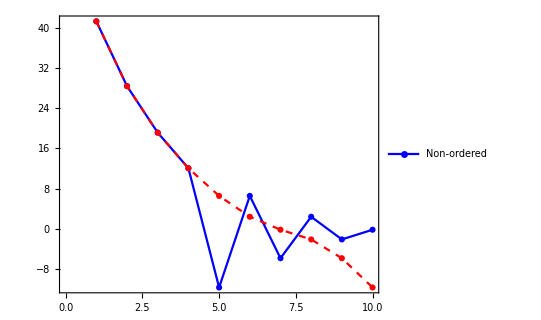

```mathematica
show[10,1]
```

Solutions of the matrix Hamiltonian

```mathematica
(* The eigenvalues for the bosonic Hamiltonian - given in decreasing order, from the highest value to the lowest, nu matter how the default return list is computed *)
sol02Ordered[n_,q_]:=Sort[Eigenvalues[boson0[n,q]],Greater];
sol13Ordered[n_,q_]:=Sort[Eigenvalues[boson1[n,q]],Greater];
(* The eigenvalues for the bosonic Hamiltonian - given in the actual order prefered by the Mathematica's implementation *)
sol02Pure[n_,q_]:=Eigenvalues[boson0[n,q]];
sol13Pure[n_,q_]:=Eigenvalues[boson1[n,q]];
```

```mathematica
N[sol02Ordered[10,1]]
N[sol02Pure[10,1]]
```

{41.2502,28.3619,19.1292,12.0478,6.55402,2.40978,-0.170188,-2.09878,-5.83432,-11.6496}

{41.2502,28.3619,19.1292,12.0478,-11.6496,6.55402,-5.83432,2.40978,-2.09878,-0.170188}

Evolution of λ with the ratio q

```mathematica
lambda02Ordered[n_,q_,id_]:=sol02Ordered[n,q][[id]];
lambda13Ordered[n_,q_,id_]:=sol13Ordered[n,q][[id]];
lambda02Pure[n_,q_,id_]:=sol02Pure[n,q][[id]];
lambda13Pure[n_,q_,id_]:=sol13Pure[n,q][[id]];
```

## Plot the solution with certain id, for a given truncation order N, evaluated at q∈[0,3]

### The unordered plot

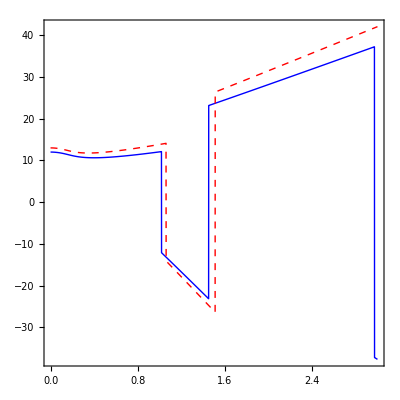

```mathematica
plotSolution[n_,id_]:=Plot[{lambda02Pure[n,q,id],lambda13Pure[n,q,id]},{q,0,3},Frame->True,Axes->False,AspectRatio->1,PlotStyle->{{Thick,Blue},{Thick,Red,Dashed}}];
plotSolution[10,4]
```

### The ordered plot

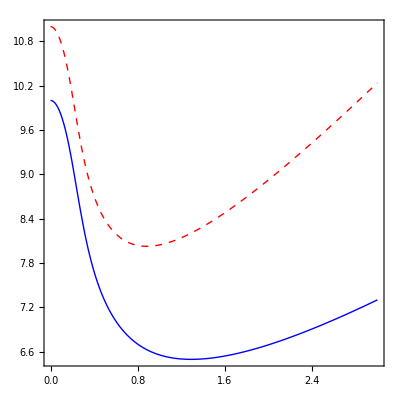

```mathematica
plotSolutionOrdered[n_,id_]:=Plot[{lambda02Ordered[n,q,id],lambda13Ordered[n,q,id]},{q,0,3},Frame->True,Axes->False,AspectRatio->1,PlotStyle->{{Thick,Blue},{Thick,Red,Dashed}}];
plotSolutionOrdered[10,5]
```

## Comparing the python lambda ordering vs. Mathematica’s own solution

```mathematica
mydata=Import["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/quadraticHamiltonianDiagonalization/Reports/output_lambdas.txt","CSV"];
```

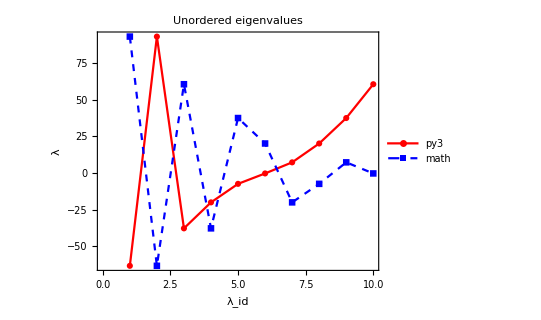

```mathematica
showPy3vsMath[n_,q_]:=ListPlot[{mydata[[1]],sol02Pure[n,q]},Joined->True,Frame->True,Axes->False,LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},AspectRatio->0.8,PlotStyle->{{Red,Thick},{Blue,Thick,Dashed}},PlotMarkers->Automatic,FrameStyle->Directive[Black,Thick],FrameLabel->{"λ_id","λ"},PlotLegends->{"py3","math"},PlotLabel->"Unordered eigenvalues"];
showPy3vsMath[10,3]
```

```mathematica
(*Plot[{lambdaQ[4,1,p],lambdaQ[4,2,p],lambdaQ[4,3,p],lambdaQ[4,4,p],Sqrt[1-4p^2]},{p,0,0.5},AspectRatio->1,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],LabelStyle->{Black,20,Bold,FontFamily->"Times New Roman"},FrameLabel->{"q",Subscript["λ","i"]},PlotLegends->Placed[{"λ_1","λ_2","λ_3","λ_4","ω"},{0.15,0.7}],ImageSize->Medium,PlotStyle->Thick]*)
```

## Compare ordered python vs math

```mathematica
pyOrder={92.9866284440667,60.523122397055594,37.48898843221059,20.14651146852637,7.299868861429066,-0.2591964451096819,-7.349549128738182,-19.966598392395504,-37.67282690716859,-63.19694872987617};
```

{92.9866,60.5231,37.489,20.1465,7.29987,-0.259196,-7.34955,-19.9666,-37.6728,-63.1969}

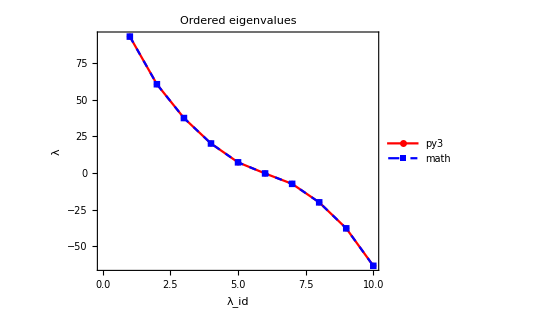

```mathematica
ListPlot[{pyOrder,N[sol02Ordered[10,3]]},Joined->True,Frame->True,Axes->False,LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},AspectRatio->0.8,PlotStyle->{{Red,Thick},{Blue,Thick,Dashed}},PlotMarkers->Automatic,FrameStyle->Directive[Black,Thick],FrameLabel->{"λ_id","λ"},PlotLegends->{"py3","math"},PlotLabel->"Ordered eigenvalues"]
```